```mathematica
mat={{1,-1},{1,1}}
```

{{1,-1},{1,1}}

```mathematica
Eigensystem[mat]
```

{{1+ⅈ,1-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

```mathematica
mat . {1,0}
```

{1,1}

{-1,-1}

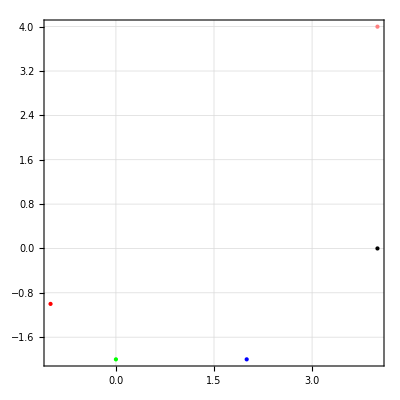

```mathematica
Po={-1,-1}
Show[Graphics[{PointSize-> Large,Red,Point[Po]}],Graphics[{PointSize-> Large,Green,Point[mat.Po]}],Graphics[{PointSize-> Large,Blue,Point[mat.mat.Po]}],Graphics[{PointSize-> Large,Black,Point[mat.mat.mat.Po]}],
Graphics[{PointSize-> Large,Pink,Point[mat.mat.mat.mat.Po]}],
AspectRatio-> 1,GridLines-> Automatic,Frame-> True]
```

```mathematica
lista={};
For[i=1,i≤5,i++,
P={0,RandomReal[]};
AppendTo[lista,{P}];
For[j=1,j≤15,j++,
P=mat.P;
AppendTo[lista⟦i⟧,P]];
]
```

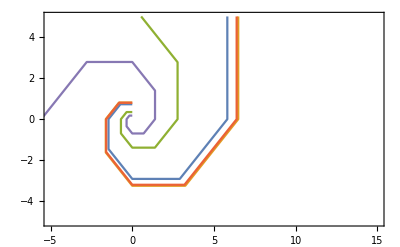

```mathematica
ListPlot[lista,Joined->True,Frame-> True,PlotRange->{{-5,15},{-5,5}}]
```

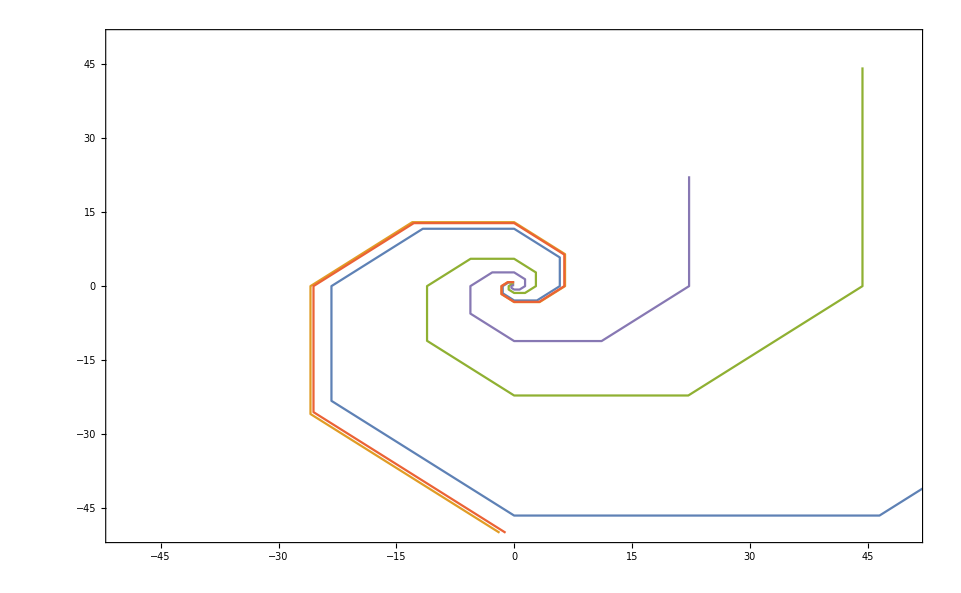

```mathematica
ListPlot[lista,Joined->True,Frame->True,PlotRange->{{-50,50},{-50,50}}]
```

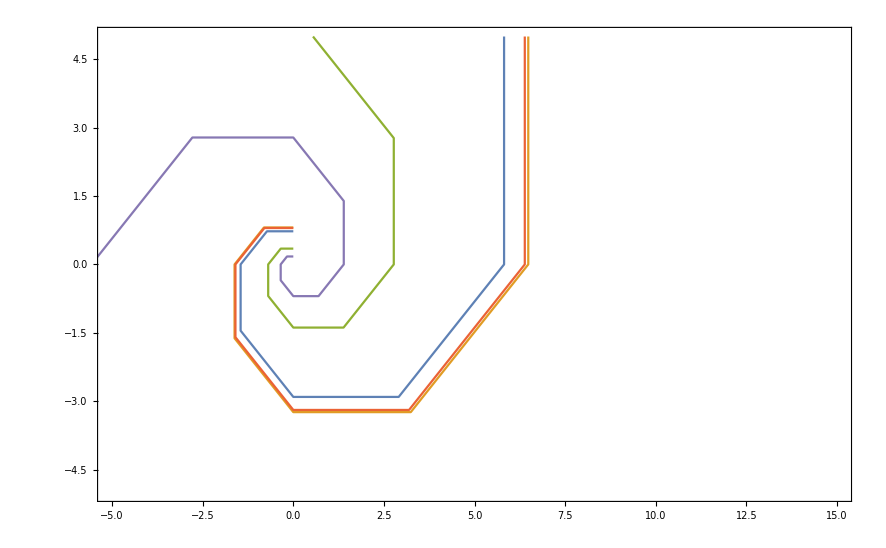

-Graphics-